# What Makes Wolfram QuantumFramework Unique: A Verified Showcase

Wolfram QuantumFramework is a quantum laboratory built into the Wolfram Language. The objects of quantum theory, states, operators, channels, measurements, circuits, are exact symbolic expressions: they carry free parameters, compose with one another in closed form, and answer questions about themselves through one uniform interface. A computation here typically ends in a formula, the propagator U(t) of a time-dependent Hamiltonian, an optimization landscape you can differentiate, an entanglement entropy S(t) you can solve, rather than a table of numbers. The same objects run in any finite dimension, qubits, qutrits, spin-j multiplets, N-level systems, and they reach outward as well, to OpenQASM, to device transpilation, to real quantum hardware. Its natural habitat is the computation whose deliverable is insight: a closed form, an exact threshold, a verified physical statement.

This document makes that concrete as five claims, each developed through worked examples:

Symbolic-first, exact algebra by default. Time-dependent Hamiltonians solved to closed-form propagators, a control Hamiltonian recovered from a target evolution, an exact QAOA landscape, a many-body entanglement entropy as a formula in time.

One object model spans all of quantum theory. Channels, POVMs, bosonic Fock space, and phase-space quasi-probabilities are the same kind of object as a gate, a master equation solves symbolically for every state and rate at once, and a thousand-qubit stabilizer state is one more object; the model stores the basis on every object, runs in any finite dimension, and closes with a full state-tomography loop.

A quantum object is an ordinary Wolfram Language expression. Built-ins like Plot and Reduce apply to it directly, precisely because nothing about it is special.

Every object draws itself. Bloch spheres, amplitude charts that carry the phases, measurement histograms, circuit diagrams, and the tensor network behind a circuit, each a one-call property of the object it depicts.

Open, inspectable, and an interoperability hub. The simulation engine's contraction order exposed as an option; OpenQASM in and out natively; transpilation to a device target; submission to a real QPU, with IBM as the worked example.

The claims build on one another, symbolic objects at the base and real hardware at the summit, so we begin with the algebra everything else inherits.

## Claim 1: Symbolic-first, exact algebra by default

Key feature: symbolic algebra pervades the whole object model, not one function. The building blocks you reach for, a state (QuantumState), a Hamiltonian (QuantumOperator), its time evolution (QuantumEvolve), and a circuit (QuantumCircuitOperator), are each fully symbolic, and they compose into exact closed-form results. We take them in that order, starting with the simplest: a state whose amplitudes are symbols.

### A symbolic state

A QuantumState can carry free symbols. Build one with symbolic amplitudes and read them back:

```mathematica
psi = QuantumState[{Cos[α], Sin[α] Exp[I β]}];
psi["StateVector"] // Normal
```

{Cos[α],ⅇ^(ⅈ β) Sin[α]}

The amplitudes return exactly as {cos α,  e^iβ sin α}, symbols intact.

The same object reports its exact Bloch geometry (ComplexExpand treats α and β as real):

```mathematica
psi["BlochVector"] // ComplexExpand // FullSimplify
```

{Cos[β] Sin[2 α],Sin[2 α] Sin[β],Cos[2 α]}

The Bloch vector returns exactly as (sin 2α cos β,  sin 2α sin β,  cos 2α): the full geometry as functions of α and β, without committing to numbers.

### A time-dependent symbolic Hamiltonian

Hamiltonians need not be static. The following is a spin-1/2 in a magnetic field that rotates in the xy-plane at frequency ω, on top of a static z-field, the standard model of magnetic resonance and of a driven qubit. It is explicitly time-dependent: t is QF's time variable, and it appears inside the operator.

```mathematica
H = ω0/2 QuantumOperator["Z"] +
    Ω/2 (Cos[ω t] QuantumOperator["X"] + Sin[ω t] QuantumOperator["Y"])
```

QuantumOperator[…]

Because the field direction turns, H does not commute with itself at different times, so the propagator is not simply e^(-i∫H dt); it needs genuine time-ordering. Check the non-commutativity directly:

```mathematica
Hm[t_] := Normal[H["Matrix"]] /. t -> t;
Commutator[Hm[t1], Hm[t2], Dot]//FullSimplify
```

{{-1/2 ⅈ Ω^2 Sin[(t1-t2) ω],1/2 (-ⅇ^(-ⅈ t1 ω)+ⅇ^(-ⅈ t2 ω)) Ω ω0},{1/2 (ⅇ^(ⅈ t1 ω)-ⅇ^(ⅈ t2 ω)) Ω ω0,1/2 ⅈ Ω^2 Sin[(t1-t2) ω]}}

The commutator is nonzero, its diagonal carrying ∓i/2 Ω^2 sin: this is the genuinely hard, time-ordered case, not a disguised static problem.

### Its propagator, in closed form

QuantumEvolve integrates the time-dependent Schrodinger equation i ∂_t U=H(t) U and returns the propagator U(t) symbolically. (Verified here: U(0)=I and i U'(t)-H(t) U(t)=0 exactly.)

```mathematica
U = QuantumEvolve[H, None]
```

QuantumOperator[…]

Simplify its matrix under real parameters and Ω>0:

```mathematica
Assuming[{ω ∈ Reals, ω0 ∈ Reals, Ω > 0, t ∈ Reals},
  FullSimplify[ComplexExpand[Normal[U["Matrix"]]]]] // MatrixForm
```

(ⅇ^(-1/2 ⅈ t ω) (Cos[1/2 t √(Ω^2+(ω-ω0)^2)]+(ⅈ (ω-ω0) Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2))) | -(ⅈ ⅇ^(-1/2 ⅈ t ω) Ω Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2))
-(ⅈ ⅇ^((ⅈ t ω)/2) Ω Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2)) | ⅇ^((ⅈ t ω)/2) (Cos[1/2 t √(Ω^2+(ω-ω0)^2)]-(ⅈ (ω-ω0) Sin[1/2 t √(Ω^2+(ω-ω0)^2)])/(√(Ω^2+(ω-ω0)^2))))

The matrix returns exactly as the lab-frame Rabi propagator, written here with the detuning δ≡ω-ω_0 and the generalized Rabi frequency Ω_R≡√(Ω^2+δ^2):

U(t)=(e^(-iωt/2)(cos (Ω_R t)/2+i δ/Ω_R sin (Ω_R t)/2) | - i e^(-iωt/2) Ω/Ω_R sin (Ω_R t)/2
- i e^(iωt/2) Ω/Ω_R sin (Ω_R t)/2 | e^(iωt/2)(cos (Ω_R t)/2-i δ/Ω_R sin (Ω_R t)/2))

The e^(∓iωt/2) factors are the rotating-frame phases; the cos and sin of Ω_R t/2 are the dressed-state oscillations. The physically meaningful readout is the transition probability (|⟨1|U(t)|0⟩|)^2:

```mathematica
amp = Normal[U["Matrix"]][[2, 1]];
Assuming[{ω ∈ Reals, ω0 ∈ Reals, Ω > 0, t ∈ Reals},
  FullSimplify[ComplexExpand[Abs[amp]^2]]]
```

(Ω^2 Sin[1/2 t √(Ω^2+(ω-ω0)^2)]^2)/(Ω^2+(ω-ω0)^2)

The result is the textbook Rabi formula, P_(0→1)(t)=Ω^2/(Ω^2+δ^2) sin^2 (t/2 √(Ω^2+δ^2)). On resonance (ω=ω_0, so δ=0) this is sin^2 (Ωt/2): complete Rabi flopping between |0⟩ and |1⟩. The oscillation rate √(Ω^2+δ^2) is the generalized Rabi frequency, the dressed-state gap in the rotating frame, here recovered as a closed-form function of the drive detuning and strength.

### When the closed form needs special functions: Landau-Zener

The rotating-field propagator was elementary, but symbolic evolution is not confined to elementary functions. Sweep the energy bias linearly through an avoided crossing at rate v with a constant gap Δ, the Landau-Zener model, again time-dependent and non-commuting:

```mathematica
HLZ = v t/2 QuantumOperator["Z"] + Δ/2 QuantumOperator["X"]
```

QuantumOperator[…]

Ask QuantumEvolve for the propagator, and pull out one of the special functions it is built from:

```mathematica
ULZ = QuantumEvolve[HLZ, None];
FullSimplify[Normal[ULZ["Matrix"]]]//TraditionalForm
```

(ⅇ^(-1/4 ⅈ t^2 v) (ⅈ Δ^2)/(8 v)1/21/2 ⅈ t^2 v | (-1^(1/4) Δ ⅇ^(-1/4 ⅈ t^2 v) (ⅇ^(1/2 ⅈ t^2 v) (ⅈ Δ^2)/(8 v) 1-(ⅈ Δ^2)/(4 v) (ⅈ Δ^2)/(4 v)-1(-1/2+ⅈ/2) t √v-(ⅈ Δ^2)/(4 v) 1/2-(ⅈ Δ^2)/(8 v) -(ⅈ Δ^2)/(4 v)(1/2+ⅈ/2) t √v))/(√2 π √v (csch((π Δ^2)/(8 v))-sech((π Δ^2)/(8 v))))
-((2+2 ⅈ) √v ⅇ^(-1/4 ⅈ t^2 v) (ⅇ^(1/2 ⅈ t^2 v) (ⅈ Δ^2)/(8 v)+1/2 1-(ⅈ Δ^2)/(4 v) (ⅈ Δ^2)/(4 v)(-1/2+ⅈ/2) t √v+(ⅈ Δ^2)/(4 v) 1-(ⅈ Δ^2)/(8 v) ((1+ⅈ) t √v -(ⅈ Δ^2)/(4 v)(1/2+ⅈ/2) t √v-1-(ⅈ Δ^2)/(4 v)(1/2+ⅈ/2) t √v)))/(π Δ (csch((π Δ^2)/(8 v))-sech((π Δ^2)/(8 v)))) | (2^(-1/2-(ⅈ Δ^2)/(8 v)) (ⅈ 2^(1/2+(ⅈ Δ^2)/(4 v)) (ⅈ Δ^2)/(8 v) 1-(ⅈ Δ^2)/(4 v) (ⅈ Δ^2)/(4 v)(-1)^(3/4) t √v+2 (ⅈ Δ^2)/(4 v) 1/2-(ⅈ Δ^2)/(8 v) (-1^(1/4) t √v -(ⅈ Δ^2)/(4 v)-1^(1/4) t √v-1-(ⅈ Δ^2)/(4 v)-1^(1/4) t √v)))/(π (csch((π Δ^2)/(8 v))-sech((π Δ^2)/(8 v)))))

The output is a parabolic cylinder function D_ν(z) with index ν=- i Δ^2/4v and argument z∝√v t. The whole propagator is built from these solutions of the Weber equation, and it checks out as a genuine propagator (numerically U(0)=I, solves the Schrodinger equation, and is unitary). In the long-time limit the asymptotics of these functions collapse to the famous Landau-Zener transition probability P=e^(-π Δ^2/2v). This is symbolic evolution reaching past elementary functions to the special-function solution the physics demands.

### Designing the dynamics: recover H(t) from a target U(t)

The previous examples solved given Hamiltonians. The inverse is just as symbolic: choose a unitary trajectory U(t), and the Hamiltonian that drives it is H(t)=i U̇(t) U^†(t), the engine behind counterdiabatic driving and shortcuts to adiabaticity. Compose the target trajectory from QF's named parametric gates, a quadratically chirped Z rotation following an X rotation:

```mathematica
U = QuantumOperator["RZ"[t^2]] @ QuantumOperator["RX"[t]]
```

QuantumOperator[…]

Differentiate the trajectory as an operator, D acts on the parametric QuantumOperator directly, close it with the operator's own Dagger, and read the control field off each axis with the Pauli decomposition:

```mathematica
H = I D[U, t] @ U["Dagger"];
FullSimplify[ComplexExpand[#]] & /@ H["PauliDecompose"]
```

<|X→Cos[t^2]/2,Y→Sin[t^2]/2,Z→t,I→0|>

The controls return axis by axis: a linearly growing field t on Z, the quadrature pair 1/2 cos t^2 and 1/2 sin t^2 on X and Y, and a vanishing identity component, traceless as a control should be. Together they are the drive H(t)=t Z+1/2(cos t^2 X+sin t^2 Y) that realizes the chosen evolution, and i U̇=H U holds identically (verified). You specify the evolution gate by gate; the algebra returns the fields to apply on each axis, a closed-form inverse with no differential solver involved.

### A parametric circuit: QAOA, built entirely from a graph

QAOA is the canonical parametric circuit for optimization: one layer alternates a cost unitary e^(-iγ H_C) with a mixer e^-iθB, and we tune the two angles to maximize a classical objective. Everything below is derived from a problem graph, so nothing is hardcoded. Take the triangle, a frustrated instance where you cannot cut all three edges, and read off the classical optimum:

```mathematica
g = CompleteGraph[3];
FindMaximumCut[g]
```

{2,{{1},{2,3}}}

The classical answer is a cut of 2 of the 3 edges, one vertex against the other two. Record the vertex count for reuse:

```mathematica
n = VertexCount[g]
```

3

The MaxCut cost Hamiltonian H_C=∑_(i, j) (1-Z_i Z_j)/2 is assembled straight from the edge list, one (1-Z_i Z_j)/2 term per edge, and carries a label that will name its block in the diagram below:

```mathematica
Hc = QuantumOperator[Total[With[{id = QuantumOperator[StringJoin[ConstantArray["I", n]]]/2},
   (id - QuantumOperator["ZZ"/2, #] &) /@ (List @@@ EdgeList[g])]], "Label" -> "Hamiltonian"]
```

QuantumOperator[…]

Change g and this operator adapts to any graph.

The ansatz is built one labeled piece at a time. State prep puts every qubit in |+⟩, an equal superposition over all cuts:

```mathematica
stateprep = QuantumCircuitOperator[{StringJoin[ConstantArray["0", n]], "H" -> Range[n]}, "Label" -> "Prep"]
```

QuantumCircuitOperator[…]

The cost layer applies one ZZ(γ) rotation per edge, carrying the angle γ:

```mathematica
qcost = QuantumCircuitOperator[("R"[γ, "ZZ"] -> # &) /@ (List @@@ EdgeList[g]), "Parameters" -> {γ}, "Label" -> "Cost"]
```

QuantumCircuitOperator[…]

The mixer applies an R_X(θ) to every vertex:

```mathematica
mixer = QuantumCircuitOperator[{"RX"[θ] -> VertexList[g]}, "Parameters" -> {θ}, "Label" -> "Mixer"]
```

QuantumCircuitOperator[…]

Compose the three into one parametric layer:

```mathematica
oneLayer = QuantumCircuitOperator[{stateprep, qcost, mixer}, "Parameters" -> {θ, γ}]
```

QuantumCircuitOperator[…]

Not a single qubit index was written by hand.

The cost landscape is the expectation ⟨ψ|H_C|ψ⟩, and here QF leans on a feature worth naming: a QuantumCircuitOperator can hold states as elements. Composing the prep circuit (the ket), the operator H_C, and the prep circuit's ["Dagger"] (the bra) builds ⟨ψ|H_C|ψ⟩ as a single object, and that object draws itself:

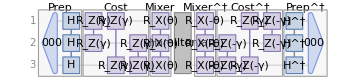

```mathematica
meanvalue = (oneLayer /* Hc /* oneLayer["Dagger"]);
meanvalue["Diagram"]
```

The diagram shows the bra-ket sandwich block by block, the labeled Prep/Cost/Mixer layer, the Hamiltonian in the middle, and the daggered layer mirrored on the right: the expectation value as a picture. Calling the same object with []["Scalar"] reads off the number, no manual inner product:

```mathematica
landscape = FullSimplify[meanvalue[]["Scalar"], Element[{γ, θ}, Reals]]
```

3/8 (3+Cos[2 γ]+2 Cos[2 θ] Sin[γ]^2-2 Sin[2 γ] Sin[2 θ])

The exact QAOA energy landscape returns as ⟨H_C⟩(γ, θ)=3/8(3+cos 2γ+2cos 2θ sin^2 γ-2sin 2γ sin 2θ), a closed form in the two angles.

```mathematica
Plot3D[landscape,{γ,0,2π},{θ,0,2π}, PlotRange -> All,
  AxesLabel -> {"γ", "θ", "cost"}, ColorFunction -> "TemperatureMap",
  PlotPoints->50]
```

-Graphics3D-

Maximize it exactly:

```mathematica
Maximize[landscape, {θ, γ}]
```

{2,{θ→-5 π-ArcTan[1/(√2)],γ→-2 (24 π-ArcTan[])}}

The maximum returns as exactly 2, with the optimal angles as closed-form algebraic numbers, and it equals FindMaximumCut[g]: because the landscape is exact, the variational optimum provably equals the true cut value, the same way a symbolic VQE expectation lands exactly on a Hamiltonian's eigenvalue rather than merely near it.

### The payoff: a full many-body computation in closed form

The same machinery scales to a genuine many-body computation. Build the 2-qubit Heisenberg Hamiltonian H=J (XX+YY+ZZ) symbolically (Hamiltonian simulation, the workhorse application of a quantum computer):

```mathematica
H = J (QuantumOperator["XX"] + QuantumOperator["YY"] + QuantumOperator["ZZ"])
```

QuantumOperator[…]

Quench the product state |01⟩ under it and display the state at time t:

```mathematica
st = QuantumEvolve[H, QuantumState["01"]];
FullSimplify[st] // TraditionalForm
```

ⅇ^(ⅈ J t) cos(2 J t)01-ⅈ ⅇ^(ⅈ J t) sin(2 J t)10

The evolved ket displays in closed form: the excitation oscillates coherently between |01⟩ and |10⟩ at angular frequency 2J, inside an overall phase e^iJt. Now read off the entanglement entropy of one qubit as a function of time, a derived, nonlinear quantity:

```mathematica
s = FullSimplify[QuantumPartialTrace[st, {2}]["VonNeumannEntropy"], t J ∈ Reals]
```

(-2 Cos[2 t J]^2 Log[Cos[2 t J]^2]+(-1+Cos[4 t J]) Log[Sin[2 t J]^2])/Log[4] b

QF returns the entire curve as a formula in t and J: the binary entropy of the two oscillating populations, zero whenever the state is a product, a full bit at the Bell points, periodic with the exchange oscillation. Because it is a formula, it can be differentiated, expanded, or solved in closed form, and the same approach extends to larger symbolic spin chains.

Plot it (at J=1):

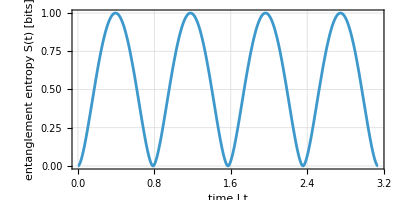

```mathematica
Plot[s /. {J -> 1, t -> t}, {t, 0, Pi},
  Frame -> True, FrameLabel -> {"time  J t", "entanglement entropy  S(t)  [bits]"},GridLines->Automatic,AspectRatio->1/2]
```

## Claim 2: One object model spans all of quantum theory

Key feature: QF gives you whole categories of object beyond unitary gates: open systems, generalized measurements, continuous-variable optics, phase space, stabilizer states, and state estimation. Two quiet generalities run underneath the whole model: every object carries its basis, and every object lives in any finite dimension. The point is scope, the range of quantum theory QF represents as objects you compute with directly.

### An open-system object: a quantum channel

A noise process is its own object, a QuantumChannel, not a gate. Take a generic pure qubit on the Bloch sphere, polar angle θ and azimuth ϕ, and confirm it is pure through the purity Tr[ρ^2], which equals 1 exactly for a pure state and drops below 1 for a mixed one:

```mathematica
psi = QuantumState[{Cos[θ/2], Exp[I ϕ] Sin[θ/2]}];
psi["Purity"] // FullSimplify
```

1

The purity is 1, as it must be for any pure state.

Send it through amplitude damping and ask how much purity is lost, as an exact function of the damping rate γ and the state:

```mathematica
FullSimplify[psi["Purity"] - QuantumChannel["AmplitudeDamping"[γ]][psi]["Purity"],
  {θ ∈ Reals, ϕ ∈ Reals, 0 <= γ <= 1}]
```

-2 (-1+γ) γ Sin[θ/2]^4

The purity loss returns exactly as 2 γ(1-γ) sin^4 θ/2. The pure input has become mixed: irreversible, non-unitary dynamics captured directly as a channel object. The loss depends only on γ and the excited-state weight sin^2 (θ/2), never on the azimuth ϕ, and it vanishes at γ=0 (no damping), at γ=1 (fully relaxed to the pure ground state), and at θ=0 (|0⟩, which damping leaves untouched).

### The master equation, solved once for every state and every rate

A channel is one snapshot of decoherence; the full dynamics is the Lindblad master equation, ρ̇=-i[H, ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i, ρ}), and QuantumEvolve solves it symbolically. Hand it a density matrix whose four entries are symbols and rates that stay symbols, and one solve answers for every qubit experiment at once. Set the physical region, the decay operator σ_-=|0⟩⟨1| (written as its matrix so it empties the excited state), and the all-states-at-once ρ_0:

```mathematica
$Assumptions = γ1 > 0 && γϕ >= 0 && Ω ∈ Reals && t >= 0;
σm = QuantumOperator[{{0, 1}, {0, 0}}];
ρ0 = QuantumState[Array[ρ, {2, 2}]];
```

Solve the master equation for a qubit with level splitting Ω, energy relaxation at γ_1 (jump operator √γ_1 σ_-), and pure dephasing at γ_ϕ (jump operator √γ_ϕ Z):

```mathematica
ρt = QuantumEvolve[Ω/2 QuantumOperator["Z"],
   {Sqrt[γ1] σm, Sqrt[γϕ] QuantumOperator["Z"]}, ρ0, t];
FullSimplify /@ Normal[ρt["Computational"]["DensityMatrix"]] // MatrixForm
```

(ρ[1,1]+(1-ⅇ^(-t γ1)) ρ[2,2] | ⅇ^(-1/2 t (γ1+4 γϕ+2 ⅈ Ω)) ρ[1,2]
ⅇ^(-1/2 t (γ1+4 γϕ-2 ⅈ Ω)) ρ[2,1] | ⅇ^(-t γ1) ρ[2,2])

The matrix returns exactly as the complete relaxation law for an arbitrary qubit:

ρ(t)=(ρ_11+(1-e^(-γ_1 t))ρ_22 | ρ_12 e^(-(γ_1/2+2 γ_ϕ+iΩ)t)
ρ_21 e^(-(γ_1/2+2 γ_ϕ-iΩ)t) | ρ_22 e^(-γ_1 t))

The excited population empties at γ_1, the lost weight lands on the ground state, and the coherence precesses at Ω while decaying at Γ_2=γ_1/2+2 γ_ϕ: every experiment on every qubit, in one matrix. With T_1=1/γ_1 and T_2=1/Γ_2 read off the exponents, the textbook bound between the two times is now a theorem about this solution:

```mathematica
Reduce[ForAll[{γ1, γϕ}, γ1 > 0 && γϕ >= 0, 1/(γ1/2 + 2 γϕ) <= 2/γ1]]
```

True

The reduction returns True: T_2≤2 T_1 holds for every admissible rate pair, handed over by the computation rather than quoted from a textbook, and the same Reduce asked for equality returns γ_ϕ=0 (verified): the famous factor of two is saturated exactly when dephasing vanishes.

### A generalized measurement: a POVM

Real detectors are not always projective. A POVM is a set of positive effects {E_i} summing to the identity, ∑_i E_i=I, with outcome probabilities given by the Born rule p_i=Tr[ρ E_i]; build one from your own effects with QuantumMeasurementOperator[{E1, E2, ...}]. A symmetric informationally complete POVM is the maximally symmetric case: d^2 rank-one effects E_i=1/d|ψ_i⟩⟨ψ_i| with equal pairwise overlaps (|⟨ψ_i|ψ_j⟩|)^2=1/(d+1), four outcomes on a two-level system, pointing along the vertices of a tetrahedron in the Bloch ball. Measure the generic Bloch qubit ψ from the channel example, the Born rule applied symbolically to all four effects:

```mathematica
sic = QuantumMeasurementOperator["TetrahedronSICPOVM"];
probs = FullSimplify[ComplexExpand[Tr[psi["DensityMatrix"] . Normal[#]] & /@ sic["POVMElements"]]]
```

{1/4 (1+Cos[θ]),1/12 (3-Cos[θ]-√2 Sin[θ] (Cos[ϕ]+√3 Sin[ϕ])),1/12 (3-Cos[θ]-√2 Cos[ϕ] Sin[θ]+√6 Sin[θ] Sin[ϕ]),1/12 (3-Cos[θ]+2 √2 Cos[ϕ] Sin[θ])}

The four probabilities return exactly as p_i=1/4(1+r̂·(n̂)_i), the first reading (1+cos θ)/4 and the others 1/12(3-cos θ+√2 sin θ (…)) along the remaining tetrahedron directions (n̂)_i, with r̂ the state's Bloch vector; they sum to 1 identically (verified). Pin the state to the north pole and the general formulas collapse to numbers:

```mathematica
probs /. θ -> 0
```

{1/2,1/6,1/6,1/6}

The distribution collapses to simple rationals: |0⟩ puts a half on the tetrahedron vertex nearest the pole and a sixth on each of the other three. And because the SIC is informationally complete, these four probabilities are not merely statistics of the state, they are the state: θ and ϕ can be solved back from them, which is what makes SIC measurements the natural alphabet of tomography.

### Continuous-variable quantum optics

Bosonic Fock space, not qubits. The second-order coherence at zero delay, g^(2)(0)=⟨a^†a^†a a⟩/(⟨a^†a⟩^2)=⟨n(n-1)⟩/⟨n⟩^2, is the normalized chance of detecting two photons at once; it sorts light by photon statistics, antibunched (<1, nonclassical), coherent (=1), and bunched thermal (>1).

```mathematica
g2s = <|"Fock" -> G2Coherence[FockState[1]], "Coherent" -> G2Coherence[CoherentState[20][1.5]],
  "Thermal" -> G2Coherence[ThermalState[1.0, 20]]|>
```

<|Fock→0,Coherent→1.,Thermal→1.99968|>

Each class lands where the formula predicts: zero for the single photon, one for the laser, two for thermal light. The three values chart directly:

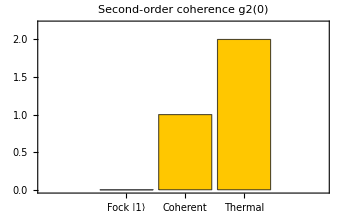

```mathematica
BarChart[g2s, ChartLabels -> {"Fock |1⟩", "Coherent", "Thermal"},
  PlotLabel -> "Second-order coherence g2(0)", Frame -> True, PlotRange -> {0, 2.2}]
```

### A phase-space quasi-probability

The Wigner function is the phase-space quasi-probability W(x, p)=1/π∫⟨x-y | ρ | x+y⟩ e^(2ipy) dy. It integrates to 1 like a probability density but, unlike one, can go negative, and that negativity is a signature of nonclassicality with no classical or gate-circuit analogue.

```mathematica
w = WignerRepresentation[FockState[1], {-4, 4}, {-4, 4}, "GridSize" -> 90];
w[0, 0]
```

-0.318252

Verified: W(0,0)=-0.318<0. The single photon has a negative dip at the origin. The whole surface plots directly:

```mathematica
Plot3D[w[x, p], {x, -3, 3}, {p, -3, 3}, PlotRange -> All,
  AxesLabel -> {"x", "p", "W"}, ColorFunction -> "TemperatureMap",
  PlotPoints->50]
```

-Graphics3D-

### Every object carries its basis

The scope extends inward too: every state, operator, and measurement above is stored together with the basis it is written in. A basis is a stored matrix B whose rows are the basis vectors in computational coordinates, a change of basis is the similarity A_ℬ=B^-1 AB, and objects written in different bases reconcile automatically through the computational frame. About three dozen named bases ship (Bell, Fourier, Schwinger, Dirac, Gell-Mann, Wigner, MUB, SIC), and the same engine lowers non-computational measurements for OpenQASM export and supplies the magic (Bell) basis for two-qubit KAK gate compilation. Watch the representation move while the physics stays put: take the qubit |+⟩, the spread-out superposition (|0⟩+|1⟩)/√2 in the computational basis, and write it in the X basis instead:

```mathematica
QuantumState[QuantumState["+"], "X"] // TraditionalForm
```

The state renders as the single ket |x_+⟩: in its own eigenbasis |+⟩ is one basis vector, not a superposition. Same state, different coordinates.

The measurable content is untouched by any such rewriting, and nothing here is qubit-bound. Take a spin-1 particle in its m_x=+1 eigenstate, defined directly in the J_x basis:

```mathematica
mx = QuantumState[{0, 0, 1}, "JX"[1]];
mx // TraditionalForm
```

J_1^x

The state renders as the single ket |J_1^x⟩. Re-express it in the computational (J_z) basis:

```mathematica
mxZ = QuantumState[mx, "Computational"[3]];
mxZ // TraditionalForm
```

1/2 0+1/(√2)1+1/2 2

The same state spreads into a three-term superposition over the J_z levels: one ket in its own basis, a sum in the other. The named operator J_x is itself stored in its own eigenbasis, so the expectation ⟨J_x⟩=⟨ψ|J_x|ψ⟩ mixes three declared bases at once; compute it from both representations of the state:

```mathematica
<|"JX basis" -> mx["Dagger"][QuantumOperator["JX"[1]][mx]]["Scalar"],
  "Computational basis" -> mxZ["Dagger"][QuantumOperator["JX"[1]][mxZ]]["Scalar"]|>
```

<|JX basis→1,Computational basis→1|>

Both entries return as ⟨J_x⟩=1: the state in either coordinate system, the operator in a third, and QF reconciled them all; the invariant survives every change of coordinates.

### Any finite dimension: a spin-1 qutrit and a five-site ring

A spin-1 particle, an NV-center defect for instance, is a genuine three-level system. Build its zero-field-splitting Hamiltonian H=2d J_z^2+e (J_x^2-J_y^2) from QF's native spin-1 operators, with both couplings left symbolic:

```mathematica
{Jx, Jy, Jz} = QuantumOperator /@ {"JX"[1], "JY"[1], "JZ"[1]};
H = 2 d Jz^2 + e (Jx^2 - Jy^2);
H["Matrix"] // MatrixForm
```

(d+e/2 | 0 | d+e/2
0 | 2 d-e | 0
d+e/2 | 0 | d+e/2)

The operator returns fully symbolic, and its matrix displays in the basis the algebra carried along, the J_x eigenbasis: the couplings stay symbols, and the coordinates stay attached to the object.

A Hamiltonian is simplest in its energy eigenbasis, and the operator hands over its own eigenvectors. Build a basis from them and read H there:

```mathematica
QuantumOperator[H, QuantumBasis[H["Eigenvectors"]]]["Matrix"] // Normal // FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 2 d-e | 0
0 | 0 | 2 d+e)

The matrix returns exactly as diag(0,  2d-e,  2d+e): the zero-field-split spectrum in closed form, symbols intact. Building a basis from an object's own eigenvectors works in any dimension, and the spin-j operators ship natively for every j.

Dimension need not be a power of two either. A particle hopping on an N-site ring lives in an N-dimensional Hilbert space, here N=5; its hopping Hamiltonian is sparse in the site basis but, by Bloch's theorem, diagonal in the momentum (Fourier) basis:

```mathematica
n = 5;
ring = -Table[Boole[Mod[i - j, n] == 1 || Mod[j - i, n] == 1], {i, n}, {j, n}];
Normal @ Chop @ N @ Diagonal[QuantumOperator[QuantumOperator[ring], QuantumBasis["Fourier"[n]]]["Matrix"]]
```

{-2.,-0.618034,1.61803,1.61803,-0.618034}

The diagonal returns exactly the tight-binding dispersion E(k)=-2cos (2πk/N) at the five Bloch momenta, and the off-diagonal terms vanish: a five-level system, diagonalized by a named basis the same way a qubit would be.

### A stabilizer state: the state as its symmetry group

The model also spans representations: a stabilizer state is stored not as 2^n amplitudes but as the group of Pauli operators that fix it, its stabilizer generators, kept in a binary symplectic tableau. Build the GHZ state in this representation and read its generators:

```mathematica
ps = PauliStabilizer["GHZ"];
ps["PauliForm"]
```

{XXX,ZZI,IZZ}

Three Pauli strings return and determine the eight-amplitude state completely. This is the Gottesman-Knill representation, in which a Clifford gate is a constant-size rewrite of the tableau rather than a 2^n×2^n matrix product.

Pauli expectations are closed-form algebra on the generators, with no state vector anywhere:

```mathematica
<|"XXX" -> ps["Expectation", "XXX"], "ZZI" -> ps["Expectation", "ZZI"], "ZII" -> ps["Expectation", "ZII"]|>
```

<|XXX→1,ZZI→1,ZII→0|>

The two stabilizers return deterministically +1, while the unstabilized single-qubit Z is exactly unbiased, all read off by 𝔽_2 phase tracking.

The payoff of the representation is scale. Stream twenty thousand random Clifford gates onto a thousand qubits, a state whose amplitude vector would need 2^1000 entries, and time the evolution:

```mathematica
SeedRandom[1]; n = 1000;
gates = Flatten @ Table[{"H" -> RandomInteger[{1, n}], "CNOT" -> RandomSample[Range[n], 2], "S" -> RandomInteger[{1, n}]}, {6666}];
First @ AbsoluteTiming[big = PauliStabilizer[n]["ApplyCircuit", gates];]
```

1.17475

The whole gate stream folds in about half a second (0.47 s in this run): ApplyCircuit runs the tableau updates through one compiled kernel, so the cost per gate is microseconds and independent of the 2^n that never gets built. The bipartite entanglement entropy across the half-chain cut is then a closed form, S(A)=rank_𝔽_2 (generators restricted to A)-|A| (Fattal et al. 2004), exact at any qubit count:

```mathematica
big["Entropy", Range[n/2]]
```

496

The entropy returns as exactly 496 ebits of a possible 500: the random circuit has driven the chain to near-maximal, Page-like entanglement, and the value is an exact integer from an 𝔽_2 rank, not an estimate. The formalism's boundary is first-class too: a non-Clifford gate (T, or a general phase) steps outside the stabilizer group, and QF answers with a StabilizerFrame, a superposition of stabilizer states, rather than a wrong answer.

### State estimation: tomography from measured counts

Tomography is the inverse of measurement: recover an unknown state from the statistics of measurements in several bases, and it is part of the same object model. The three qubit Pauli bases X, Y, Z are mutually unbiased and together informationally complete, so their outcome frequencies pin down the density matrix (Adamson and Steinberg 2010). QF runs the whole loop. First, simulate 2000 measurement shots of an unknown state in each of the three bases:

```mathematica
SeedRandom[42];
true = QuantumState[N @ {Cos[Pi/6], Sin[Pi/6] Exp[I Pi/4]}];
data = QuantumMeasurementSimulation[true, QuantumMeasurementOperator /@ {"X", "Y", "Z"}, 2000];
Values[data]
```

{{1605,395},{1620,380},{1504,496}}

Three pairs of counts return, one per basis, the X measurement giving 1605 "+" against 395 "-" and so on: multinomially-sampled tallies, all a real experiment ever sees.

Now hand the counts to the estimator, which does linear inversion followed by maximum-likelihood, and read the reconstructed density matrix:

```mathematica
est = QuantumStateEstimate[data];
est["MaximumLikelihoodState"]["DensityMatrix"] // Normal // Chop
```

{{0.751442,0.301831-0.309314 ⅈ},{0.301831+0.309314 ⅈ,0.248558}}

The recovered ρ≈{{0.751,  0.302-0.309 i}, {0.302+0.309 i,  0.249}}, against the true {{0.75,  0.306-0.306 i}, …}. To score the reconstruction, compute its fidelity F(ρ, σ)=Tr √(√ρ σ √ρ) to the state we started from, equal to 1 exactly when the two states coincide:

```mathematica
QuantumSimilarity[true, est["MaximumLikelihoodState"]]
```

0.999985

The fidelity returns as ≈0.99998: the unknown state recovered from finite, noisy synthetic data, using nothing but counts in three bases. Past these unitary measurement bases the same basis engine continues into the over-complete operator frames, where B^-1 becomes a dual frame and a state turns into a probability vector, the mechanism behind the SIC measurement above.

## Claim 3: A quantum object is an ordinary Wolfram Language expression

Key feature: a QF object is a symbolic expression like any other in the language, with no separate runtime or data format behind it. That is the whole trick: the same obj["..."] dispatch and the same built-in functions (Plot, Reduce, NProbability, …) apply to it directly, with nothing to convert or export first. Each example below is a different WL operation flowing through a QF object.

### Property dispatch: one object, many questions

Ask one object many questions, get answers, no extra packages: here the purity Tr[ρ^2], the von Neumann entropy S=-Tr[ρ log_2 ρ], whether the state is entangled, and the concurrence C (a 0-to-1 entanglement measure, maximal for a Bell state).

```mathematica
bell = QuantumState["Bell"];
<|"Purity" -> bell["Purity"], "Entropy" -> bell["VonNeumannEntropy"],
  "EntangledQ" -> QuantumEntangledQ[bell], "Concurrence" -> QuantumEntanglementMonotone[bell, "Concurrence"]|>
```

<|Purity→1,Entropy→0 b,EntangledQ→True,Concurrence→1|>

The answers return self-labeled: the state is pure, carries zero global entropy, is entangled, and has maximal concurrence, four facts off one object.

The same dispatch returns closed forms when the state carries a symbol. A Werner state's purity and entropy as exact functions of p:

```mathematica
w = QuantumState["Werner"[p, 2]];
Simplify /@ <|"Purity" -> w["Purity"], "Entropy" -> w["VonNeumannEntropy"]|>
```

<|Purity→Abs[1-2 p+(4 p^2)/3],Entropy→((-1+p) Log[1-p]-p Log[p/3])/Log[2] b|>

Both come back as closed forms in the mixing parameter: the purity is | 1-2p+(4 p^2)/3 | and the entropy is S(p)=[(p-1)log (1-p)-plog p/3]/log 2 bits.

### Dispatch returns WL data: a Hamiltonian as an Association of Pauli strings

A property can hand back a structured Wolfram Language container. A variational quantum eigensolver writes a Hamiltonian as a sum of Pauli strings, H=∑_α h_α P_α with P_α∈{I, X, Y, Z}^(⊗n), and measures each string in its own eigenbasis; commuting strings share a measurement setting (Gokhale et al. 2020). Take the hydrogen-molecule Hamiltonian in its two-qubit form as a plain numeric matrix and ask for that decomposition:

```mathematica
H2 = QuantumOperator[{{0., 0, 0, 0}, {0, -0.2738, 0.182, 0},
                      {0, 0.182, -1.8302, 0}, {0, 0, 0, 0.1824}}];
H2["PauliDecompose"]
```

<|XX→0.091+0. ⅈ,YY→0.091+0. ⅈ,ZZ→0.5716+0. ⅈ,ZI→0.3435+0. ⅈ,IZ→-0.4347+0. ⅈ,II→-0.4804+0. ⅈ|>

The dense matrix comes back as the Association -0.4804 II+0.3435 ZI-0.4347 IZ+0.5716 ZZ+0.091 XX+0.091 YY: the six observables a VQE estimates, in an ordinary key-value container, so the measurement grouping itself (the Z strings share one setting, XX/YY another) is a Keys/Select computation away.

### Straight into Plot

A QF call goes directly inside a built-in. The concurrence of cos θ |00⟩+sin θ |11⟩ is computed by QF and drawn by the language's own Plot.

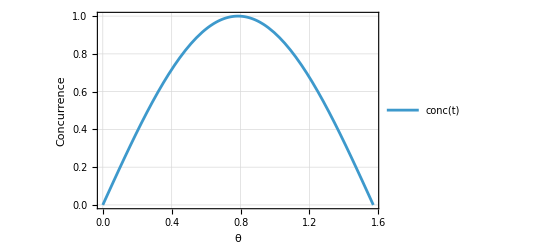

```mathematica
conc[t_?NumericQ] := QuantumEntanglementMonotone[
  QuantumState[{Cos[t], 0, 0, Sin[t]}, 2], {1}, "Concurrence"];
Plot[conc[t], {t, 0, Pi/2}, Frame -> True,
 FrameLabel -> {"θ", "Concurrence"}, PlotTheme -> "Detailed"]
```

QF also returns the closed form: concurrence =sin (2θ).

### Straight into Reduce

Get the realignment entanglement criterion of a Werner state as a symbolic function of p:

```mathematica
crit = Simplify[QuantumEntanglementMonotone[QuantumState["Werner"[p, 2]], "Realignment"], 0 < p < 1]
```

1/2 (-1+Abs[3-4 p])

Feed that QF expression straight into Reduce to solve for the entanglement threshold:

```mathematica
Reduce[crit > 0 && 0 < p < 1, p]
```

0<p<1/2

The criterion comes back as (|3-4p|-1)/2, and Reduce turns it into the exact threshold: the Werner state is entangled precisely for 0<p<1/2.

## Claim 4: Every object draws itself

Key feature: visualization is property dispatch, not a separate plotting library. Each object exposes plot properties that render through the Wolfram Language graphics stack and forward its options, so a publication figure is one call on the object it depicts. The catalog is wide: states render as Bloch vectors, amplitude and probability charts, and qudit pie and sector wheels ("PieChart", "SectorChart"); measurements as outcome histograms; stabilizer states as their binary symplectic tableau ("TableauForm"); circuits as diagrams, tensor-network graphs, and multiway and causal-graph views; adiabatic evolutions as spectrum, gap, and coupling plots ("EnergySpectrumPlot", "SpectralGapPlot", "AdiabaticCouplingPlot", "AdiabaticPathPlot" in the QuantumOptimization sub-package); the underlying TensorNetwork also renders as a hypergraph through the TensorNetworks paclet; and the phase-space objects of Claim 2 plot as Wigner surfaces. Below, one example per object kind.

### A state on the Bloch sphere

A single qubit draws its own Bloch vector:

```mathematica
QuantumState[{Cos[Pi/5], Sin[Pi/5] Exp[I Pi/3]}]["BlochPlot"]
```

-Graphics3D-

The output is a Graphics3D of the sphere with the state's arrow at polar angle 2π/5 and azimuth π/3: the geometry of the state, drawn by the state.

### Amplitudes that keep their phases

A bar chart of probabilities discards the phases; AmplitudesChart draws the complex amplitudes themselves, heights for magnitudes and colors for phases. Chart a GHZ state pushed through a quantum Fourier transform, which scrambles two real amplitudes into a phase-rich pattern:

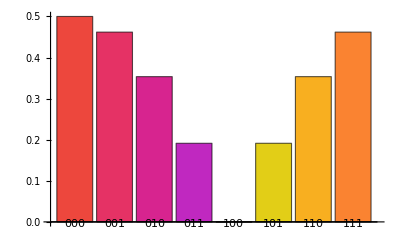

```mathematica
QuantumCircuitOperator[{"GHZ"[3], "Fourier"[3]}][]["AmplitudesChart", ChartLegends -> Automatic]
```

Eight bars return with equal-magnitude structure but a wheel of distinct phase colors keyed by the legend: magnitude and phase in one figure, the full complex state on display.

### A measurement draws its statistics

A QuantumMeasurement object charts its own outcome distribution:

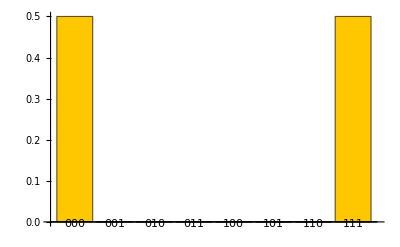

```mathematica
QuantumCircuitOperator[{"GHZ"[3], {1, 2, 3}}][]["ProbabilitiesPlot"]
```

Two bars of height 1/2 at 000 and 111: the GHZ correlations as a histogram. The hardware result in Claim 5 is the same kind of object, which is why simulated and measured statistics compare so directly there.

### A stabilizer state shows its tableau

The stabilizer states of Claim 2 have a native picture of their own: the binary symplectic tableau, the actual data structure the formalism computes on. Draw it for the GHZ state:

```mathematica
PauliStabilizer["GHZ"]["TableauForm"]
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1)

The display is the sign column beside a binary grid, dividers separating the x bits from the z bits and the destabilizer rows from the stabilizer rows; the bottom three rows are exactly the generators XXX, ZZI, IZZ in symplectic coordinates. This view is the algebra: a Clifford gate acts on the state by rewriting a few columns of precisely this grid.

### The circuit, and the network behind it

A circuit draws itself as a gate diagram:

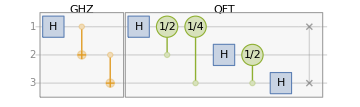

```mathematica
qcv = QuantumCircuitOperator[{"GHZ"[3], "Fourier"[3]}];
qcv["Diagram"]
```

The familiar wire-and-gate picture, Hadamard and CNOT chain into the QFT block. The same object also draws its computational anatomy, the tensor network the engine contracts:

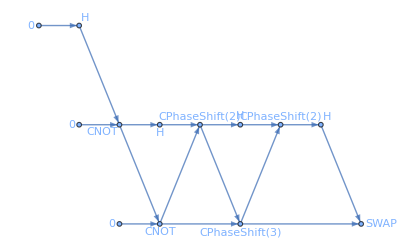

```mathematica
qcv["TensorNetworkGraph"]
```

A Graph whose vertices are the gate and state tensors and whose edges are the contracted indices: the diagram shows the physics, the network shows the computation, and Claim 5 steers the order in which that network is contracted.

The same network renders in the dual picture too, as a hypergraph in which the roles swap, every index a vertex and every tensor one hyperedge spanning its indices:

```mathematica
qcv["TensorNetwork"]["Hypergraph"]
```

-Graphics-

The result is a Hypergraph with thirteen hyperedges, one per tensor, the three |0⟩ states and the ten gates, drawn over the network's indices: the tensor-contraction picture of the same circuit, in which contracting two tensors is the merging of two hyperedges.

## Claim 5: Open, inspectable, and an interoperability hub

Key feature: openness runs in both directions. Inward, the simulation engine is not a black box: its central algorithmic choice is exposed as an option. Outward, a QF object can leave QF for the rest of the ecosystem, and foreign circuits can enter it; QuantumQASM is the single OpenQASM door, and it runs in pure Wolfram Language with no external account.

### Steer the engine: the tensor-network contraction path

Applying a circuit is, by default, a tensor-network contraction, and the order of the pairwise contractions decides the cost: every step produces an intermediate tensor, the expense is set by the largest intermediate the order ever creates (in matrix-product language, the bond dimension it forces you to carry), and a poor order can be exponentially more expensive than a good one on the very same network. QF exposes that choice as a Method sub-option: "Path" -> "Greedy" or "Optimal" (with the cost objectives "flops", "size", "write", "combo"), or an explicit list of pairwise contractions. Apply a 10-qubit GHZ circuit through a greedily chosen path and read the nonzero amplitudes:

```mathematica
ghz = QuantumCircuitOperator["GHZ"[10]];
psi = ghz[QuantumState["Register"[10]], Method -> {"TensorNetwork", "Path" -> "Greedy"}];
Most @ ArrayRules @ psi["StateVector"]
```

{{1}→1/(√2),{1024}→1/(√2)}

The state returns with exactly two nonzero amplitudes, {1}→1/(√2) and {1024}→1/(√2), that is (|0⟩)^(⊗10) and (|1⟩)^(⊗10): the GHZ state, computed through an explicitly steered contraction.

The plan itself is an inspectable object. Pull the circuit's tensor network, compute the greedy path, and draw the contraction as a tree, each node an intermediate tensor labeled by its dimensions:

```mathematica
net = ghz["TensorNetwork"];
ContractionTree[TensorNetworkContraction[net, GreedyContractionPath[net]], "Labels" -> "Dimensions"]
```

-Graphics-

The tree is the engine's execution plan: the leaves are the circuit's gate and state tensors, every internal node is one pairwise contraction, and the dimension labels trace the intermediate sizes the greedy choice keeps small, exactly the quantity a good path minimizes and a bad one lets blow up.

### Export to OpenQASM 3.0 (native, no Python)

QuantumQASM turns a circuit into the standard text format read by Qiskit, Cirq, and most hardware stacks.

```mathematica
QuantumQASM[QuantumCircuitOperator["GHZ"[3]]]
```

OPENQASM 3.0;
qubit[3] q;
bit[0] c;
U(1.5707963267948966, 0., 3.141592653589793) q[0];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[0] q[1];
ctrl(1) @ negctrl(0) @ U(3.141592653589793, 0., 3.141592653589793) q[1] q[2];

The output is a complete OpenQASM 3.0 program: a qubit[3] register, a Hadamard on q[0] written as a U rotation, and the two CNOTs as ctrl @ U gates. The native emitter writes OpenQASM 3.0, and the importer below reads OpenQASM 2.0 or 3.0 alike. A 2.0 dump is one option away through the qiskit path, QuantumQASM[qc, "Version" -> 2] (that route needs Python; the 3.0 export and all imports do not). Export needs concrete angles: a circuit with a symbolic parameter returns a Failure rather than a QASM string, so resolve parameters to numbers at this boundary while keeping them symbolic everywhere else in QF (Claims 1 and 3).

### Import foreign OpenQASM and compute with it (native, no Python)

The same door runs the other way: hand QuantumCircuitOperator an OpenQASM string authored anywhere and get back a QF circuit, parsed in pure WL, reset, controlled gates, mid-circuit measure and all. Import a four-qubit circuit that runs the optimal quantum strategy for the CHSH game:

```mathematica
qc = QuantumCircuitOperator["OPENQASM 3.0;
qubit[4] q;
bit[4] c;
reset q[0];
reset q[3];
U(1.5707963267948966, 0., 3.141592653589793) q[3];
U(1.5707963267948966, 0., 3.141592653589793) q[0];
swap q[0] q[3];
ctrl(0) @ negctrl(1) @ U(1.5707963267948966, 3.141592653589793, 3.141592653589793) q[0] q[3];
ctrl(1) @ negctrl(0) @ U(1.5707963267948966, 0., 0.) q[0] q[3];
reset q[1];
U(1.5707963267948966, 0., 3.141592653589793) q[1];
reset q[2];
U(1.5707963267948966, 0., 3.141592653589793) q[2];
U(0., 0., 0.) q[0];
ctrl(1) @ negctrl(0) @ U(1.5707963267948966, 0., 3.141592653589793) q[1] q[0];
U(0.7853981633974483, 0., 0.) q[3];
ctrl(0) @ negctrl(1) @ U(1.5707963267948966, 0., 3.141592653589793) q[2] q[3];
c[0] = measure q[0];
c[1] = measure q[1];
c[2] = measure q[2];
c[3] = measure q[3];"];
```

Once imported it is an ordinary QF object. Read its joint measurement distribution, label the four outcomes (a, x, y, b), and ask Wolfram Language for the CHSH winning probability Pr in one line:

```mathematica
NProbability[BitAnd[x, y] == BitXor[a, b], {a, x, y, b} \[Distributed] qc[]["MultivariateDistribution"]]
```

0.853553

The answer is 0.8536=cos^2 (π/8)=(2+√2)/4, exactly the Tsirelson bound, the quantum maximum for CHSH. A circuit authored in another tool became a probability distribution we query with native WL statistics.

### A hardware-aware transpilation target

QiskitTarget carries a device spec (qubit count, native gate set, connectivity), validated at construction against qiskit's own Target schema through the Python bridge. Build a 5-qubit linear-chain device and read its coupling map back:

```mathematica
target = QiskitTarget[<|"NumQubits" -> 5, "BasisGates" -> {"cx", "rz", "sx", "x"},
   "CouplingMap" -> {{0,1},{1,2},{2,3},{3,4}}|>]
```

QiskitTarget[…]

```mathematica
target["CouplingMap"]
```

{{0,1},{1,2},{2,3},{3,4}}

Hand the target to QuantumQASM as an option, and the circuit is transpiled to that backend's native gates and connectivity:

```mathematica
QuantumQASM[QuantumCircuitOperator["GHZ"[3]], "Target" -> target]
```

The GHZ circuit comes back rewritten for the device: the Hadamard compiled into rz/sx rotations, the CNOTs as cx on physical qubits $0, $1, $2, every move allowed by the coupling map.

### Submit to a real IBM QPU, and compare to the exact result

With an IBM account connected through ServiceConnect["IBMQuantumPlatform"], IBMJobSubmit sends a circuit to the hardware asynchronously and returns an IBMJob handle. A QPU job needs a circuit that ends in a measurement; in QF a list of qubit indices placed in the circuit is exactly that, so {1, 2, 3} measures all three qubits. Build the measured GHZ circuit, submit it, and check the status:

```mathematica
qc = QuantumCircuitOperator[{"GHZ"[3], {1, 2, 3}}];
job = IBMJobSubmit[qc, "ibm_fez", "Shots" -> 4096]
```

IBMJob[…]

```mathematica
job["Status"]
```

Queued

The handle returns immediately with status "Queued" while the job waits in line on the device. The same circuit runs exactly in the Wolfram Language by just applying it:

```mathematica
wl = qc[]
```

QuantumMeasurement[…]

The result is a QuantumMeasurement with probabilities 1/2 at 000 and 1/2 at 111. Once the job completes, the hardware outcome comes back as the same kind of QuantumMeasurement object, decoded into the same qubit order:

```mathematica
qpu = job["Refresh"][]
```

QuantumMeasurement[…]

This run returned 4096 shots from ibm_fez. Because the two results are the same kind of object, hardware noise is one chart away, the exact and measured probabilities paired per basis state:

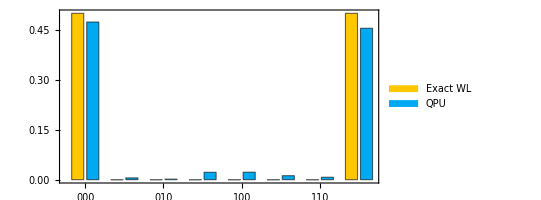

```mathematica
BarChart[Transpose[Values @* KeySort /@ {wl["Probabilities"], qpu["Probabilities"]}],
  AspectRatio -> 1/2, Frame -> True, ChartLegends -> {"Exact WL", "QPU"},
  PlotLabels -> Keys[wl["Probabilities"]]]
```

The exact bars are 1/2 at 000 and 111 and zero elsewhere; the device returned 0.428 at 000 and 0.420 at 111, with the remaining 15% spread thinly over the six bitstrings the exact state forbids. That gap, read bar by bar off one figure, is the device noise.

## Where This Leaves Us

Five claims, each cashed out in executed code. Symbolic algebra carried dynamics to closed form: the Rabi propagator of a rotating drive, a Landau-Zener sweep expressed in parabolic cylinder functions, a control Hamiltonian recovered exactly from its target evolution, a QAOA landscape whose maximum provably equals the true cut, the entanglement entropy of a quench as a function of time. One object model held the rest of the theory: channels, POVMs, Fock space, and phase space; a master equation solved once for every initial state and every rate, with T_2≤2 T_1 arriving as a theorem rather than a remembered rule; a basis and a dimension on every object; a thousand-qubit stabilizer state with an exact half-chain entropy of 496 ebits; a state reconstructed from measured counts at fidelity 0.99998. Because these objects are ordinary Wolfram Language expressions, the language computed with them directly, and each of them drew itself. And the same objects left the system: out to OpenQASM and back, through a transpiler to a device's native gates, and onto a physical quantum processor, whose 4096-shot histogram stands in this document next to the exact distribution it approximates.

Behind all five claims is one mechanism: quantum objects that are exact symbolic expressions compose, with each other and with the entire language. The distance from writing a Hamiltonian to reading its closed form, or to running it on hardware, is a handful of composable calls. A result that is a formula can be differentiated, reduced, or pushed to a limit; a result that is a circuit is already in the format the rest of the quantum ecosystem speaks.

The next steps are the reader's: change the graph under the QAOA section, raise the spin past 1, swap damping for dephasing, point the last section at a different backend. The document re-derives itself.

Setup. Evaluate once before the cells:

```mathematica
Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"];
Needs["Wolfram`TensorNetworks`"];
```

Every cell was executed as shown (Wolfram Language 15.0, Wolfram/QuantumFramework 2.0.0) and every stated output is the captured result, including the hardware run on ibm_fez; reproducing the transpilation cells needs a Python installation with qiskit, and the hardware cells an IBM Quantum account.